## Projekt IX1303 Algebra och Geometri, VT2021 Mohamad Abou Helal mohamaah@kth . se

Assignment 1:
Hitta en allmän lösning till dynamiska systemet x_(k+1)=Ax_k där A utgörs av den
stokastiska matrisen för Hertz Rent a Car i exemplet ovan (Tal 4.9.16 i Lay).

16.[M] In Detroit, Hertz Rent A Car has a fleet of about
2000 cars . The pattern of rental and return locations is given
by the fractions in the table below . On a typical day, about
how many cars will be rented or ready to rent from the
downtown location?

```mathematica
T=({{.90, .01, .09}, {.01, .90, .01}, {.09, .09, .90}})
```

{{0.9,0.01,0.09},{0.01,0.9,0.01},{0.09,0.09,0.9}}

```mathematica
Soultion:
 MatrixT ={{0.90 , 0.01 , 0.09} , {0.01 , 0.90, 0.01},{0.09 , 0.09 , 0.90}};
MatrixT // MatrixForm
```

(0.9 | 0.01 | 0.09
0.01 | 0.9 | 0.01
0.09 | 0.09 | 0.9)

```mathematica
MatrixTDistributionI= MatrixForm[ MatrixT - IdentityMatrix[3]]
```

(-0.1 | 0.01 | 0.09
0.01 | -0.1 | 0.01
0.09 | 0.09 | -0.1)

```mathematica
ReinforcementMatrix = {{ -0.1, 0.01, 0.09,0}, {0.01, -0.1, 0.01, 0},{0.09, 0.09, -0.1, 0}};
RowReducedMatrix = MatrixForm[RowReduce[ReinforcementMatrix]]
```

(1 | 0. | -0.919192 | 0.
0 | 1 | -0.191919 | 0.
0 | 0 | 0 | 0)

```mathematica
MatrixForm[{.919192,0.191919,1}]
```

(0.919192
0.191919
1)

```mathematica
result=MatrixForm[{.919192,0.191919,1}/(.919192+0.191919+1)]
```

(0.435407
0.090909
0.473684)

```mathematica
Numberofcars=0.090909×2000
```

181.818

Number of cars that will be available for rent is 182.

Assignment 2:
Avgör om följande uppsättning polynom utgör en bas för vektorrummet 𝕡_3.
{5-3t+4 t^2+2 t^3,9+t+8 t^2-6 t^3, 6-2t+5 t^2,t^2}

```mathematica
c={{5,-3,4,2},{9,1,8,-6},{6,-2,5,0},{0,0,1,0}};
```

```mathematica
MatrixForm[c]
```

(5 | -3 | 4 | 2
9 | 1 | 8 | -6
6 | -2 | 5 | 0
0 | 0 | 1 | 0)

```mathematica
Det[c]
```

0

Assignment 3:
Ange diagonalmatrisen D och matriserna P och P-1 som används för diagonalisering av A
                                                            A=(-6 | 4 | 0 | 9
-3 | 0 | 1 | 6
-1 | -2 | 1 | 0
-4 | 4 | 0 | 7)

```mathematica
b={{-6,4,0,9},{-3,0,1,6},{-1,-2,1,0},{-4,4,0,7}}
```

{{-6,4,0,9},{-3,0,1,6},{-1,-2,1,0},{-4,4,0,7}}

```mathematica
MatrixForm[b]
```

(-6 | 4 | 0 | 9
-3 | 0 | 1 | 6
-1 | -2 | 1 | 0
-4 | 4 | 0 | 7)

```mathematica
Matrix= DiagonalMatrix[Eigenvalues[b]];
```

```mathematica
MatrixForm[Matrix]
```

(5 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | 1)

```mathematica
q=Transpose[Eigenvectors[b]]
```

{{2,6,1,2},{1,-3,1,-1},{-1,0,1,-7},{2,4,0,2}}

```mathematica
MatrixForm[q]
```

(2 | 6 | 1 | 2
1 | -3 | 1 | -1
-1 | 0 | 1 | -7
2 | 4 | 0 | 2)

```mathematica
qInv=Inverse[q]
```

{{-5/14,2/7,1/14,3/4},{2/21,-1/7,1/21,0},{17/21,2/7,-2/21,-1},{1/6,0,-1/6,-1/4}}

```mathematica
MatrixForm[qInv]
```

(-5/14 | 2/7 | 1/14 | 3/4
2/21 | -1/7 | 1/21 | 0
17/21 | 2/7 | -2/21 | -1
1/6 | 0 | -1/6 | -1/4)

```mathematica
Quit
```

Assignment 4:
Lös grafiskt ekvationssystemetttPiecewise[{{x+2y+3z, = 1}, {2x+4y+7z, = 2}, {3x+7y+11z, = 8}}]dvs plotta planen i R^3 och se om det finns någon lösning

```mathematica
equation1st= ContourPlot3D[x+2y+3z==1,{x,-30,30}, {y,-30,30}, {z,-30,30}]
```

-Graphics3D-

```mathematica
equation2nd= ContourPlot3D[2x+4y+7z==2,{x,-30,30}, {y,-30,30}, {z,-30,30}]
```

-Graphics3D-

```mathematica
equation3rd=ContourPlot3D[3x+7y+11z==8,{x,-30,30}, {y,-30,30}, {z,-30,30}]
```

-Graphics3D-

```mathematica
Show[equation1st,equation2nd, equation3rd]
```

-Graphics3D-

```mathematica
graphic=ContourPlot3D[{x+2y+3z==1,2x+4y+7z==2,2x+4y+7z==2},{x,-5,5},{y,-5,5},{z,-5,5},BoundaryStyle->{2->None,{1,2}->{RGBColor[0.501961, 1, 1],Thick,Dashed}}]
```

-Graphics3D-

```mathematica
Show[graphic, ViewPoint->Front]
```

-Graphics3D-

```mathematica
solution={x,y,z}/.Solve[{x+2y+3z==1,2x+4y+7z==2,3x+7y+11z==8},{x,y,z}]
```

```mathematica
{{-9,5,0}}
```

Assignment 5:
Visa att kolumnerna i matris A är ortogonala.   
A=(-6 | -3 | 6 | 1
-1 | 2 | 1 | -6
3 | 6 | 3 | -2
6 | -3 | 6 | -1
2 | -1 | 2 | 3
-3 | 6 | 3 | 2
-2 | -1 | 2 | -3
1 | 2 | 1 | 6)

```mathematica
x={{-6,-3,6,1},{-1,2,1,-6},{3,6,3,-2},{6,-3,6,-1},{2,-1,2,3},{-3,6,3,2},{-2,-1,2,-3},{1,2,1,6}};
x//MatrixForm
```

(-6 | -3 | 6 | 1
-1 | 2 | 1 | -6
3 | 6 | 3 | -2
6 | -3 | 6 | -1
2 | -1 | 2 | 3
-3 | 6 | 3 | 2
-2 | -1 | 2 | -3
1 | 2 | 1 | 6)

```mathematica
z1=x[[All,1]];
z2=x[[All,2]];
z3=x[[All,3]];
z4=x[[All,4]];
```

```mathematica
column12=z1.z2
column13=z1.z3
column14=z1.z4
column23=z2.z3
column24=z2.z4
column34=z3.z4
```

0

0

0

«3 more identical outputs»

step solution:
the first step showed the columns in the matrix  are orthogonal, in this case the scaling product is equal to 0 then I prove that the columns in the matrix are orthogonal.

Assignment 6:
Hitta den radreducerade trappstegsmatrisen(rref)till matrisen (2 | 4 | 8
4 | 5 | 1
7 | 9 | 3)Har matrisen
någon redundans?

```mathematica
K={{2,4,8},{4,5,1},{7,9,3}};
K//MatrixForm
```

(2 | 4 | 8
4 | 5 | 1
7 | 9 | 3)

```mathematica
RowReduce[K]//MatrixForm
```

(1 | 0 | -6
0 | 1 | 5
0 | 0 | 0)

solution :
 I am using RowReduce to get this matrix

Assignment 7:
Lös grafiskt ekvationssystemetPiecewise[{{x-2y=, 3}, {3x+5y, =17}}]dvs  plotta linjerna i ℝ^2(och se om det finns någon lösning.

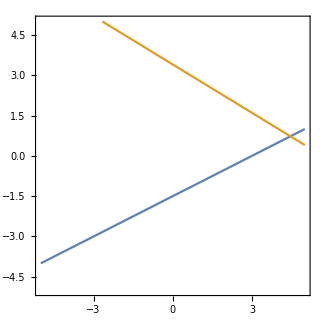

```mathematica
ContourPlot[{x-2y==3, 3x+5y==17},{x,-5,5}, {y, -5, 5}]
```

Assignment 8:
Givet matriserna A=(3 | 2 | 4
7 | 12 | 0
2 | 5 | 2) B=(5 | 8 | 7
6 | 4 | 9
10 | 1 | 0) c=(5 | 22 | 5
5 | 9 | 7
6 | 8 | 2)
beräkna matriserna A−B+C,ABC och CBA.

```mathematica
Amatrix ={{3,2,4},{7,12,0},{2,5,2}};
Bmatrix={{5,8,7},{6,4,9},{10,1,0}};
Cmatrix={{5,22,5},{5,9,7},{6,8,2}};
```

```mathematica
subtractionAndplus=Amatrix-Bmatrix+Cmatrix
```

{{3,16,2},{6,17,-2},{-2,12,4}}

```mathematica
subtractionAndplus//MatrixForm
```

(3 | 16 | 2
6 | 17 | -2
-2 | 12 | 4)

```mathematica
multi=Amatrix.Bmatrix.Cmatrix
MatrixForm[multi]
```

{{749,2110,665},{1997,4546,1577},{844,2134,684}}

(749 | 2110 | 665
1997 | 4546 | 1577
844 | 2134 | 684)

```mathematica
multiplication=Cmatrix.Bmatrix.Amatrix
MatrixForm[multiplication]
```

{{2018,3175,1294},{1260,1874,828},{1096,1750,620}}

(2018 | 3175 | 1294
1260 | 1874 | 828
1096 | 1750 | 620)

Assignment9 :
  Givet vektorerna u = 2 i + 3 j - 2 k , V = 4 i - j - k och  w = -4 i - j + 2 k , beräkna vektortrippelprodukten u×(v×w)

```mathematica
Uvektor={2,3,-2};
Vvektor={4,-1,-1};
Wvektor={-4,-1,2};
```

```mathematica
first= 2*-4 +3*-1+-2*2
```

-15

```mathematica
second=2*4+3*-1+(-2*-1)
```

7

```mathematica
Final=first* Vvektor- second*Wvektor
```

{-32,22,1}

Solution :
  Uvektor x (Vvektor x Wvektor) = (Uvektor . Wvektor) * Vvektor - (Uvektor . Vvektor)* Wvektor .
     Uvektor . Wvektor = Ui * Wi + Uj*Wj + Uk*Wk
Uvektor . Vvektor = Ui*Vi + Uj*Vj + Uk*Vk

Assignment 10:
Visa grafiskt varför följande system saknar lösning.Piecewise[{{3x+4y-z, =8}, {6x+8y-2z, =3}}]

```mathematica
ContourPlot3D[{3 x+4 y-z==8,6 x+8 y-2 z==3},{x,-5,5},{y,-5,5},{z,-5,5}]
```

-Graphics3D-

Solution :
 obviously the two planes are parallel and thus they do not intersect in any point, thus the system is lacking a solution .